Q3 : Solve the equation  x ln (x) - 3 x + 10 = 6, both symbolically and numerically .

```mathematica
sol=Solve[x Log[x]-3 x+10==6,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-4/ProductLog[-4/ⅇ^3]},{x→-4/ProductLog[-1,-4/ⅇ^3]}}

```mathematica
{x1,x2}=x/. sol
```

{-4/ProductLog[-4/ⅇ^3],-4/ProductLog[-1,-4/ⅇ^3]}

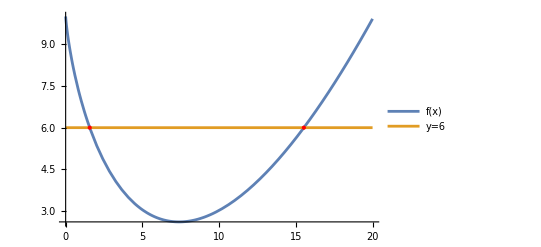

```mathematica
Show[Plot[{x Log[x]-3 x+10,6},{x,0,20}, PlotLegends->{"f(x)","y=6"},PlotRange->All],Graphics[{Red,PointSize[Large],Point[{#,6}&/@{x1,x2}]}]]
```

Numerical Solver

```mathematica
nsol = NSolve[x Log[x]-3 x+10==6,x]
{nsol1,  nsol2} = x/.nsol
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1.56883},{x→15.5229}}

{1.56883,15.5229}

```mathematica
root1 = FindRoot[x Log[x]-3 x+10==6,{x, 1}]
root2 = FindRoot[x Log[x] -3x +10 ==6, {x, 20}]
{root1,root2}=(x/. {root1,root2})
```

{x→1.56883}

{x→15.5229}

{1.56883,15.5229}

Differences

```mathematica
nsol1 -x1
nsol1-root1
nsol2 -x2
nsol2 - root2
```

0.

0.

5.32907×10^-15

5.32907×10^-15